# Classical Entropy (Shannon Entropy)

This  is  a demonstration material accompanying the corresponding YouTube video.

Episode 49. Classical Entropy (Shannon Entropy)

Episode 50. Quantum Entropy (Von Neumann Entropy)

## What is it?

Let X be a random variable.

Let p(x) be the probability distribution for X to take value x.

The Shannon entropy is defined by

H(X)≡H({p(x)}):=-Σ_x p(x)log p(x) .

### Example

```mathematica
pp=Normalize[{1,3,1,5,3,4},Total]
```

```mathematica
ent=ShannonEntropy[pp]
```

```mathematica
ent//N
```

## Meaning

Entropy is a measure of uncertainty, or the information we acquire when know about X.

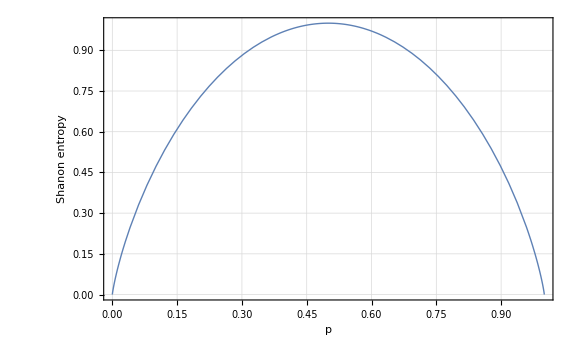

Figure 1. The Shannon entropy H({p,1−p}) associated with a binary probability distribution {p(0)=p,p(1)=1−p} of a random variable with values in {0,1}.

## Relative Entropy

Suppose that {p(x)} and {q(x)} are two probability distributions of the same random variable X with values in {x}.

The relative Shannon entropy or simply relative entropy of {p(x)} to {q(x)} (or the Kullback-Leibler divergence of {p(x)} from {q(x)}) is defined by

H({p(x)}∥{q(x)}):=Σ_x p(x) log (p(x))/(q(x))=-H({p(x)})-Σ_x p(x)logq(x).

The relative entropy (also known as Kullback-Leibler divergence) is a measure of the closeness of two probability distributions.

### Example

Consider two probability distributions.

```mathematica
pp=Normalize[{1,3,1,5,3,4},Total]
```

```mathematica
qq=Normalize[{1,3,2,4,1,1},Total]
```

Calculate the (classical) relative entropy between the two probability distributions

```mathematica
rel=ShannonEntropy[pp,qq]
```

```mathematica
rel//N
```

### “Cautionary Example”

Consider an evil dice with strongly biased probability distribution.

```mathematica
pp=Normalize[{1,2,2,4,3,0},Total]
```

Here is another probability distribution.

```mathematica
ϵ=1/100;
δ=Append[Table[-ϵ,5],5ϵ];
qq=pp+δ
```

The two probability distributions look similar. Indeed, the classical fidelity between them is reasonably high.

```mathematica
ClassicalFidelity[pp,qq]//N
```

Nevertheless, the relative entropy of qq to pp diverges.

```mathematica
ShannonEntropy[qq,pp]
```

Note that relative entropy is asymmetrical about the two input arguments, and the relative entropy of pp to qq is finite.

```mathematica
ShannonEntropy[pp,qq]//N
```

## Mutual Information

So far, we have considered a single random variable. Let us now consider two random variables X and Y .

Suppose that they randomly take values from the sets {x} and {y}, respectively, governed by the joint probability distribution p(x,y).

### Joint Entropy

The joint Shannon entropy or simply joint entropy  associated with p(x,y) is defined by

H(X,Y )≡H({p(x, y)})=−Σ_(x,y)p(x,y)logp(x,y).

### Conditional Entropy

The Shannon entropy of X conditional on knowing Y or simply conditional entropy of X on Y,

H(X|Y ):=H(X,Y )−H(Y ),

where, note that H(Y) refers to the probability distribution

p(y)=Σ_x p(x,y) .

It is the amount of uncertainty still remaining about X given that we know the value of Y.

### Mutual Information

If X and Y are statistically independent, then learning the value of Y does not help know about X at all.

The difference between the initial amount of uncertainty about X and the amount of uncertainty about X remaining after learning the value of Y would quantify the correlation between X and Y.

The mutual information of X and Y , and denote it by H(X:Y ) is defined by

H(X:Y ):=H(X)−H(X|Y )≡H(Y)-H(Y|X) .

It quantifies the correlation between X and Y.

### Examples

Consider a classical joint probability distribution  p_(i j):=p(x_i,y_j) for i=1,2,… and j=1,2,… associated with two random variables X and Y.

```mathematica
pp=RandomReal[{0,1},{6,6}];
pp/=Total[Flatten@pp];
pp//MatrixForm
```

The mutual information between the two variables is given as follows.

MutualInformation[pp]

Consider two statistically independent random variables.

```mathematica
p=Normalize[RandomReal[{0,1},6],Total]
q=Normalize[RandomReal[{0,1},4],Total]
```

The joint probability is given by the dyadic product of the two probability distributions.

```mathematica
pq=Dyad[p,q];
pq//MatrixForm
```

The mutual information is expected to vanish.

```mathematica
MutualInformation[pq]//Chop
```

Now, consider two anti-correlated random variables.

```mathematica
pp=Normalize[RandomReal[{0,1},6],Total];
pp=Chop@Reverse@DiagonalMatrix@pp;
MatrixForm[pp]
```

```mathematica
MutualInformation[pp]
```

## Summary

### Keywords

Shannon entropy

Relative entropy

Conditional entropy

Mutual information

### Functions

ShanonEntropy

MutualInformation

### Related Links

Section 7.1 of the Quantum Workbook (2022, 2023)

Tutorial: Shannon Entropy

Full List of Demonstrations in YouTube Videos